```mathematica
(*/////////////////ввод параметров///////////////////*)
pg=10000000;
H=50;
F=10000000;
m=0.2;
k=50*9.86923*10^-16;
mu=0.05;
βg=5*10^(-10);
βc=2*10^(-10);
q0=-10/3600/24;
qi=50/3600/24;
ps=2000000;
βstar=m*βg+βc;
R=Sqrt[F/Pi];
V=Pi*R^2*H;
Γ=2*Pi*R*H;
```

```mathematica
(*/////////////////граничное условие номер 1///////////////////*)
(*|V|β^*(d<p>)/dt=Subscript[Σq, i]*)
P1[t_]=DSolve[{V*βstar*P'[t]==50*q0,P[0]==pg},P[t],t][[1,1,2]]//Simplify;
Print["Решение: P(t) = ",P1[t]];
t1=Solve[P1[t]==ps,t][[1,1,2]]/3600/24;
Print["а)Время, через которое давление в пласте снизится до давления насыщения 20 атм: ",t1," суток."];
Print["б)Необходимо внести ", Abs[50*q0/qi]," скважин."];
```

Решение: P(t) = 1.×10^7-0.0385802 t

а)Время, через которое давление в пласте снизится до давления насыщения 20 атм: 2400. суток.

б)Необходимо внести 10 скважин.

```mathematica
(*/////////////////граничное условие номер 2///////////////////*)
(*|V|β^*(d<p>)/dt+|Γ|Subscript[U, n]=Subscript[Σq, i]*)
```

Решение: P(t) = 9.98534×10^6+14659.3 ⅇ^(-2.63179×10^-6 t)

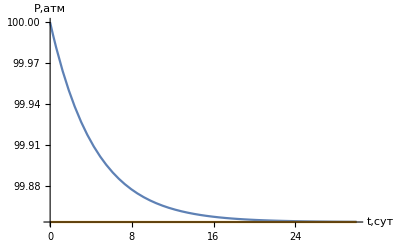

Уровень, на который выходит среднее пластовое давление: 99.8534 атм, значит давление никогда не достигнет давления насыщения

а)никогда б)0

```mathematica
alp2=k/mu/(H/2);
Un2=alp2*(P[t]-pg);
P2[t_]=DSolve[{V*βstar*P'[t]+F*Un2==50*q0,P[0]==pg},P[t],t][[1,1,2]]//Simplify;
Print["Решение: P(t) = ",P2[t]];
lim=Limit[P2[t],t->Infinity];
Plot[{P2[3600*24*t]/100000,lim/100000},{t,0,30},PlotRange->All,AxesLabel->{"t,сут","P,атм"}]
Print["Уровень, на который выходит среднее пластовое давление: ",lim/100000, " атм, значит давление никогда не достигнет давления насыщения"];
Print["а)никогда б)0"];
```

```mathematica
(*/////////////////граничное условие номер 3///////////////////*)
```

Решение: P(t) = -8.66479×10^6+1.86648×10^7 ⅇ^(-2.06701×10^-9 t)

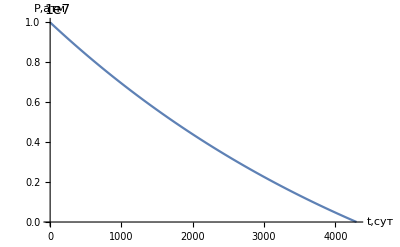

а) Время, через которое давление в пласте снизится до давления насыщения 20 атм: 3133.96 суток.

б) Необходимо внести 6 скважин.

```mathematica
alp3=k/mu/R;
Un3=alp3*(P[t]-pg);
P3[t_]=DSolve[{V*βstar*P'[t]+Γ*Un3==50*q0,P[0]==pg},P[t],t][[1,1,2]]//Simplify;
Print["Решение: P(t) = ",P3[t]];
tt=Solve[P3[t]==0,t][[1,1,2]]/86400;
Plot[P3[3600*24*t],{t,0,tt},AxesLabel->{"t,сут","P,атм"}]
Limit[P3[t],t->Infinity];
t3=Solve[P3[t]==ps,t][[1,1,2]]/86400;
Print["а) Время, через которое давление в пласте снизится до давления насыщения 20 атм: ",t3," суток."];
P[t_,nn_]=DSolve[{V*βstar*P'[t]+Γ*Un3==50*q0+nn*qi,P[0]==pg},P[t],t][[1,1,2]]//Simplify;
Print["б) Необходимо внести ", Round[Reduce[Limit[P[t,nn],t->Infinity]>ps,nn][[2]]]," скважин."];
```